```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/czhou/Projects/BEM2D/resources/testNumericTools

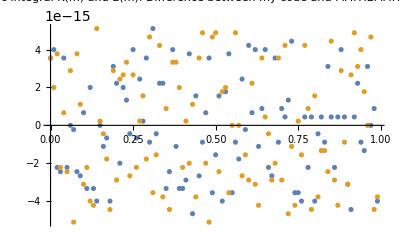

```mathematica
(*  ================== TEST1 ================== *)
myCode=Import["ellipticIntegral.txt","Table"];(*load output data from my code*)
mList = myCode⟦All,1⟧;
myEllipticK=myCode⟦All,2⟧;
myEllipticE=myCode⟦All,3⟧;
(* plot difference between my code and mathematica built-in*)
ListPlot[{Transpose@{mList,(myEllipticK-EllipticK/@mList)},Transpose@{mList,(myEllipticE-EllipticE/@mList)}},
PlotRange->All,PlotLabel->"Elliptic integral K(m) and E(m): \nDifference between my code and MATHEMATICA built-in"]
```

```mathematica
(*  ================== TEST2 ================== *)
f[x_]:=Cos[10 x]Exp[-x];(* define function to be integrate over [0,1]*)
tstar=0.2;
Integrate[f[x]Log[tstar-x],{x,0,tstar}];
analyticLogsingularIntegral =%+Integrate[f[x]Log[x-tstar],{x,tstar,1}];(*analytic result *)
analyticGaussLegendreIntegral = Integrate[f[x],{x,0,1}];(*analytic result *)
```

```mathematica
Print["Analytic Integration of f[t] over [0,1] = ", N[analyticGaussLegendreIntegral,20]];
Print["Analytic Integration of f[t]Log[|t-t_s|] over [0,1] = ",NumberForm[Re@analyticLogsingularIntegral,20{1,1}]," (t_s = 0.2)"];
```

Analytic Integration of f[t] over [0,1] = -0.0068580659146036957933

Analytic Integration of f[t]Log[|t-t_s|] over [0,1] = 0.10877465222776890000 (t_s = 0.2)

```mathematica
myCode=Import["quadratureIntegral.txt","Table"];(*load output data from my code*)
order= myCode⟦All,1⟧;
gaussLegendre=myCode⟦All,2⟧;
logSingular=myCode⟦All,3⟧;
(* see header for different situation , Subscript[t, s]= 0.5 *)
Join[{{"m-point rule","Use GaussLegendre for\n\t∫_0^1 f(t)dt","Use LogSingular for \n∫_0^1 f(t)ln|t_s-t|dt","Use GaussLegendre for\n∫_0^1 f(t)ln|t_s-t|dt"}},myCode];
NumberForm[MatrixForm@%,{16,16}]
```

(m-point rule | Use GaussLegendre for
	∫_0^1 f(t)dt | Use LogSingular for 
∫_0^1 f(t)ln|t_s-t|dt | Use GaussLegendre for
∫_0^1 f(t)ln|t_s-t|dt
0 | 0 | 0 | 0
1 | 0.1720498124845380 | 0.0869084085637365 | -0.6114136508187650
2 | -0.2163948176967240 | 0.2375009197875380 | 0.2949414950089800
3 | 0.0856164957136288 | 0.0833317014422914 | 0.0900407162616730
4 | -0.0223070876643719 | 0.1108511249695850 | 0.1001288497112900
5 | -0.0054794560602606 | 0.1086812868972260 | 0.1030481287947560
6 | -0.0069343849991142 | 0.1087772693079850 | 0.1043158864474140
7 | -0.0068552068612884 | 0.1087746036625880 | 0.1053034549393430
8 | -0.0068581425413858 | 0.1087746528317830 | 0.1060079806746500
9 | -0.0068580643904105 | 0.1087746522231040 | 0.1065245853222410
10 | -0.0068580659376164 | 0.1087746522277810 | 0.1069121433612580
11 | -0.0068580659143379 | 0.1087746522277690 | 0.1072092521409030
12 | -0.0068580659146060 | 0.1087746522277680 | 0.1074415014249650
13 | -0.0068580659146037 | 0.1087746522277690 | 0.1076262163275780
14 | -0.0068580659146038 | 0.1087746522277690 | 0.1077753896014200
15 | -0.0068580659146036 | 0.1087746522277690 | 0.1078975026940050
16 | -0.0068580659146038 | 0.1087746522277690 | 0.1079986747486640
17 | -0.0068580659146035 | 0.1087746522277690 | 0.1080834021259710
18 | -0.0068580659146037 | 0.1087746522277700 | 0.1081550443353060
19 | -0.0068580659146040 | 0.1087746522277690 | 0.1082161498495980
20 | -0.0068580659146037 | 0.1087746522277690 | 0.1082686787819870)

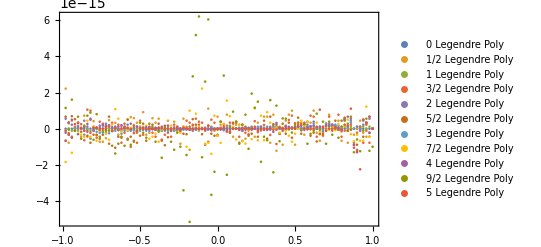

```mathematica
(*  ================== TEST3 ================== *)
myCode=Import["legendrePoly.txt","Table"];(*load output data from my code*)
xList = myCode⟦All,1⟧;
(* my code : legendre poly of order = 0, 1/2, 1, 3/2, ... , 9/2 , 5 *)
myLPoly=myCode⟦All,2;;-1⟧; 
(* MATHEMATIC built-in : legendre poly of order = 0, 1/2, 1, 3/2, ... , 9/2 , 5 *)
analyticPoly =Transpose@Table[N[ LegendreP[i,#]&/@xList],{i,0,5,1/2}];
(* plot difference between my code and MATHEMATICA *)
ListPlot[Table[Transpose@{xList,(myLPoly-analyticPoly)⟦All,i⟧},{i,1,11}],PlotRange->Full,
PlotLegends->Table[If[Mod[i,2]==0,ToString[i/2],ToString[i]<>"/2"]<>" Legendre Poly",{i,0,11}],Frame->True,Axes->False
]
```